## Fluctuation dissipation relation as equilibrium condition (detailed balance) for FP

```mathematica
gb = E^(-u[x]/T);
(* langevin: dx = - mu D[u[x],x] + Sqrt[2 a] dW;  FP stazionaria associata : *)
fpeq = 0==a D[p[x],{x,2}]+ mu D[p[x]D[u[x],x],x]
Simplify[fpeq/.{p[x]->gb,p'[x]->D[gb,x],p''[x]->D[gb,{x,2}]}] (* nota come si può raccogliere il fattore (a-mu T) *)
Solve[fpeq/.{p[x]->gb,p'[x]->D[gb,x],p''[x]->D[gb,{x,2}]},a]
```

0==a p''[x]+mu (p'[x] u'[x]+p[x] u''[x])

(ⅇ^(-u[x]/T) (a-mu T) (-u'[x]^2+T u''[x]))/T^2==0

{{a→mu T}}

## Generazione dati

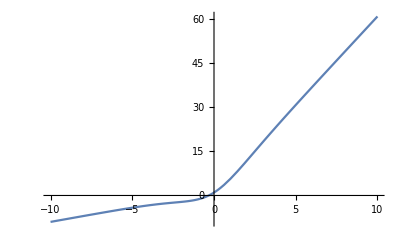

```mathematica
(* setup *)
ftrue[x_]:=1+x(1+5(1+E^(-x))^(-1)); (* modello "vero" dal quale si generano i dati *)
atrue=1; (* In realtà qualunque a > 0 si comporta nello stesso modo; questo è un po' il "problema" di questa funzione obiettivo, ma anche la feature che crea dei minimi con una grande differenza di curvature lungo b; ovviamente è stata scelta in maniera artificiale perché avesse sia minimi molto piccati che minimi molto piatti *)
btrue=5;
fmod[x_,a_,b_]:=x(1+b(1+E^(-a x))^(-1))+a^2; (* NOTA: puoi provare ad aggiungere questo termine a^2 come "penalità" per eliminare gli infiniti minimi con a>0 *)
loss[x_,y_,a_,b_]:=(y -fmod[x,a,b])^2; (* questa è solo la parte quadratica, senza somma o normalizzazione*)
gradloss[x_,y_,a_,b_]:={D[(y -fmod[x,a,b])^2,a],D[(y -fmod[x,a,b])^2,b]} ;
Plot[ftrue[x],{x,-10,10}]
```

```mathematica
(* generate a sample from ftrue*)
nn=30;
ll=20;
ntot=nn ll; (*number of datapoints*)
xs = Table[xi-Floor[nn/2],{ xi,1,nn}];
fi=Table[N[ftrue[x/.(x->xs[[i]])]],{i,1,Length[xs]}];
eps=3;
epss = RandomReal[{-eps,eps},ll*Length[fi]];
data=Table[{xs[[i]],Table[fi[[i]]+epss[[i+j]],{j,0,ll-1}]},{i,1,Length[fi]}];

(******genero dati per l'errore di generalizzazione************)
nnp= Floor[N[nn/5]];
llp = Floor[N[ll/5]];
ntotp=nnp llp; (*number of datapoints*)
xsp = Table[xi-Floor[nnp/2],{ xi,1,nnp}];
fip=Table[N[ftrue[x/.(x->xsp[[i]])]],{i,1,Length[xsp]}];
epssp = RandomReal[{-eps,eps},llp*Length[fip]];
datap=Table[{xsp[[i]],Table[fip[[i]]+epssp[[i+j]],{j,0,llp-1}]},{i,1,Length[fip]}];
lossp[a_,b_]:=(1/ntotp)*Sum[ Sum[(datap[[i,2]][[j]]-fmod[datap[[i,1]],a,b])^2,{j,1,llp}],{i,1,nnp}];(*loss function per il validation set*)
(************************************************************)
```

## Visualizzo il minimo positivo per vedere se è buono

a (n opt): 0.945497 b (n opt): 4.99995

-Graphics3D-

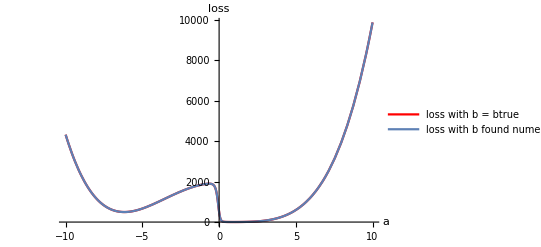

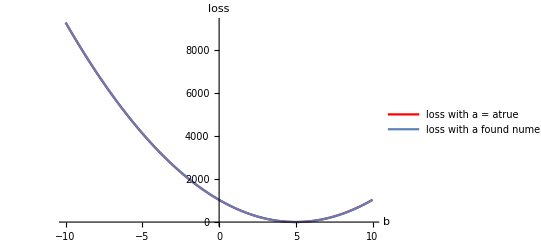

```mathematica
(*calcolo la loss function su tutto il set di dati, in funzione dei parametri*)
loss[a_,b_]:=(1/ntot)* Sum[ Sum[(data[[i,2]][[j]]-fmod[data[[i,1]],a,b])^2,{j,1,ll}],{i,1,nn}];

(*Trovo ilm minimo reale della funzione: DEBUG: non è il vero minimo, se confronti la loss function calcolata sul valore vero usato nella generazione dei dati si vede abbastanza chiaramente; i vincoli su x e y come li hai scelti? *)
areal=x/.Last[ FindMinimum[{loss[x,y],Abs[x]<=1.5atrue &&Abs[y]<=1btrue},{x,y}]];
breal=y/.Last[ FindMinimum[{loss[x,y],Abs[x]<=1.5 atrue &&Abs[y]<=1btrue},{x,y}]];
Print["a (n opt): ",areal," b (n opt): ",breal]
l=10;
Plot3D[loss[a,b],{a,-l,l},{b,-l,l}, AxesLabel->{"a","b"},PlotRange->All]
Show[
Plot[loss[a,btrue],{a,-l,l}, AxesLabel->{"a","loss"},PlotRange->All,PlotLegends->{"loss with b = btrue"},PlotStyle->Red],
Plot[loss[a,breal],{a,-l,l}, AxesLabel->{"a","loss"},PlotRange->All,PlotLegends->{"loss with b found numerically"}]
]

Show[
Plot[loss[atrue,b],{b,-l,l}, AxesLabel->{"b","loss"},PlotRange->All,PlotLegends->{"loss with a = atrue"},PlotStyle->Red],
Plot[loss[areal,b],{b,-l,l}, AxesLabel->{"b","loss"},PlotRange->All,PlotLegends->{"loss with a found numerically"}]
]
```

## Cerco il minimo negativo per verificare il crossing

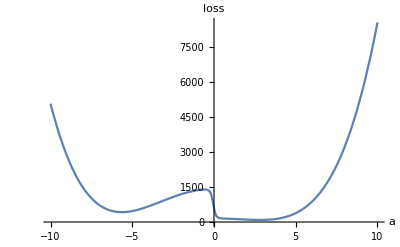

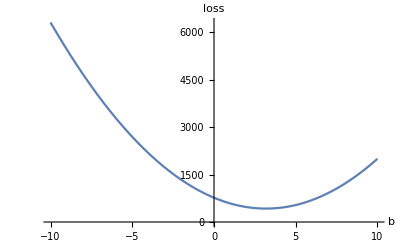

arealmin, brealmin: -5.63639 3.18065

```mathematica
(*Trovo ilm minimo negativo della funzione*)
arealmin=x/.Last[ FindMinimum[{loss[x,y],x<0 },{x,y}]];
brealmin=y/.Last[ FindMinimum[{loss[x,y],x<0 },{x,y}]];
Plot[loss[a,brealmin],{a,-l,l}, AxesLabel->{"a","loss"}]
Plot[loss[arealmin,b],{b,-l,l}, AxesLabel->{"b","loss"}]
Print["arealmin, brealmin: ", arealmin," ",brealmin]
```

## Genero il punto di partenza

```mathematica
a0 =RandomReal[];
b0=RandomReal[];
(*a0 =-5;
b0=3;*)
Print["a0, b0: ", a0," ",b0]
```

a0, b0: 0.131025 0.199092

## Training tramite SGD

```mathematica
(* IPERPARAMETRI DEL SGD *)
maxite =30000;
eta =0.0001;
bsize =10;

(* costruisco il vettore dei parametri che ottimizzo, tengo tutti le iterazioni per la visualizzazione *)
v = Table[{0,0},{ite,1,maxite}];
lossvalues=Table[0,{ite,1,maxite}]; (* per visualizzazione *)
totlossvalues=Table[0,{ite,1,maxite}]; (* sarebbe la loss usata nel GD *)
v[[1]]={a0,b0};
(* SGD loop **************************************************************)
(* nota: faccio il caso semplice del ciclo for, si può sostituire con un while per controllare se sta raggiungendo la convergenza *)
For[ite=2,ite<=maxite, ite++,
If[Mod[ite,10000]==0, Print["ite: ",ite, "/ ", maxite]];
ai = v[[ite-1]][[1]];
bi= v[[ite-1]][[2]];

(* sceglie il nuovo minibatch *)
xidxs =RandomInteger[{1,nn},bsize];
yidxs=RandomInteger[{1,ll},bsize]; (* nota che si fa così solo per il modo in cui ho costruito i dati, in generale non devi scegliere x e y in maniera indipendente!*)
xis =Table[ data[[xidxs[[bidx]],1]], {bidx,1,bsize}];
yis = Table[data[[xidxs[[bidx]],2]][[yidxs[[bidx]] ]],{bidx,1,bsize}];


(* solo per visualizzazione; calcolo la loss function per il minibatch *)  
lossvalues[[ite]]= 1/bsize 
 Sum[
N[loss[xis[[bidx]],yis[[bidx]], ai,bi]],
{bidx,1,bsize}
];

(* calcola il gradiente medio della loss rispetto ai parametri *) 
gradlossvector= 1/bsize 
 Sum[
(gradloss[xis[[bidx]],yis[[bidx]], z1,z2]/.{z1->ai,z2->bi}),
{bidx,1,bsize}
];

(* calcola l'incremento *)
dai =eta gradlossvector[[1]];
dbi =eta gradlossvector[[2]];
v[[ite]]={ai-dai, bi-dbi};
If[Mod[ite,10000]==0, Print[v[[ite]]]];
]
```

ite: 10000/ 30000

{-5.52331,3.12537}

ite: 20000/ 30000

{-5.71973,3.16608}

ite: 30000/ 30000

{-5.59181,3.19302}

## Training tramite SDE

```mathematica
etasgd =eta;
timestep=etasgd;
maxtimes=2000;
bsizesgd =bsize;
vc = Table[{0,0},{ite,1,maxtimes}];
vc[[1]]={a0,b0};



(*calcolo l'hessiano, lo valuto su tutto il set e nel punto di minimo nello spazio dei parametri(che conosco)*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};


(*vauluto l'hessiano nel minimo reale*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
sqrthesslossmin=MatrixPower[ hesslossmin, 1/2];
Print[N[hesslossmin],"*"];
Print[Eigenvalues[hesslossmin],"*"];
Print[N[sqrthesslossmin]];

(*calcolo il gradiente su tutto il set di dati*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b}

(*calcolo la dinamica*)
For[ite=2,ite≤maxtimes, ite++,
Z={RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]};
Zscale= sqrthesslossmin.Z;
ai = vc[[ite-1]][[1]];
bi= vc[[ite-1]][[2]];
vc[[ite]][[1]]= ai-gradlosstot[x,y][[1]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[1]]*Sqrt[timestep]/.{x->ai,y->bi};
vc[[ite]][[2]]= bi-gradlosstot[x,y][[2]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[2]]*Sqrt[timestep]/.{x->ai,y->bi};
If[Mod[ite,100]==0, Print[ite, ", ", vc[[ite]]]];
]
```

{{8250.83,10194.1},{10194.1,49444.3}}*

{51829.,5866.15}*

{{84.4287,33.5057},{33.5057,219.822}}

100, {-5.6619,1.72098}

200, {-5.56219,4.77268}

300, {-5.46036,4.72541}

400, {-5.34136,4.48558}

500, {-5.36575,2.94697}

600, {-4.80884,1.02648}

700, {-5.48415,0.0784996}

800, {-5.08723,3.02184}

900, {-5.28492,3.14476}

1000, {-5.09748,2.27671}

1100, {-6.06794,3.65119}

1200, {-6.24943,5.79626}

1300, {-6.3636,3.6494}

1400, {-5.55267,4.06342}

1500, {-5.27779,5.14926}

1600, {-5.5663,5.53925}

1700, {-5.98704,5.74012}

1800, {-8.2866,16.2517}

1900, {-7.54268,10.1169}

2000, {-6.33336,5.19372}

## Training tramite GD

```mathematica
maxite2=1002;
eta = 0.0001;
vgd = Table[{0,0},{ite,1,maxite2}];
vgd[[1]]={a0,b0};
For[ite=2,ite<=maxite2, ite++,
ai = vgd[[ite-1]][[1]];
bi= vgd[[ite-1]][[2]];

(* calcola l'incremento *)
dai =eta gradlosstot[x,y][[1]]/.{x->ai,y->bi};
dbi =eta gradlosstot[x,y][[2]]/.{x->ai,y->bi};
vgd[[ite]]={ai-dai, bi-dbi};
If[Mod[ite,100]==0, Print[ite, ", ", vgd[[ite]]]];
]
```

100, {0.80768,3.10925}

200, {1.01817,4.17404}

300, {1.10442,4.62399}

400, {1.13064,4.81442}

500, {1.13116,4.8963}

600, {1.12173,4.93282}

700, {1.10901,4.95027}

800, {1.09571,4.95957}

900, {1.08287,4.96529}

1000, {1.07086,4.96935}

## Correnti di probabilità

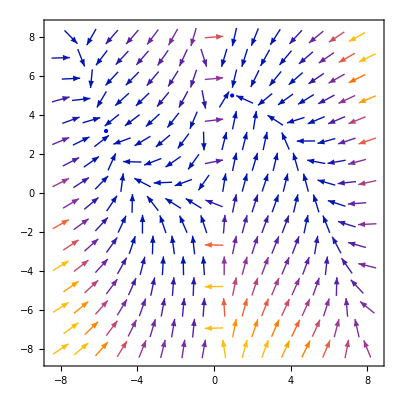

```mathematica
U[a_,b_]:= Log[loss[x,y]]/.{x->a,y->b};
T= 100;
Pstat[a_,b_]:=Exp[-U[x,y]/T]*loss[x,y]/.{x->a,y->b}; 
partialx[a_,b_]:=-D[loss[x,y],x]*Pstat[x,y]-(eta)/(bsize)*(hesslossmin[[1]][[1]]*D[loss[x,y]*Pstat[x,y],x]+hesslossmin[[1]][[2]]*D[loss[x,y]*Pstat[x,y],y])/.{x->a,y->b};
partialy[a_,b_]:=-D[loss[x,y],y]*Pstat[x,y]-(eta/bsize)*(hesslossmin[[2]][[1]]*D[loss[x,y]*Pstat[x,y],x]+hesslossmin[[2]][[2]]*D[loss[x,y]*Pstat[x,y],y])/.{x->a,y->b};


J[a_,b_]:={partialx[x,y],partialy[x,y]} /.{x->a,y->b};
r=8;
vplot=VectorPlot[J[a,b],{a,-r,r}, {b,-r,r}];
g=Graphics[{PointSize[Large],Blue,Point[{areal,breal}]}];
locmin=Graphics[{PointSize[Large],Blue,Point[{arealmin,brealmin}]}];
Show[vplot,g, locmin]
```

## Confronto i due algoritmi

parametri stimati, SGD: {0.955584,5.0045}

parametri stimati, SDE: {0.845002,4.72524}

a0, b0: -0.5 4

atrue, btrue: 1 5

areal, breal: 0.945497 4.99995

In-sample error, SGD: 2.36099

In-sample error, GD: 2.43782

In-sample error, SDE: 6.00623

Out-of-sample error, SGD: 1.90546

Out-of-sample error, GD: 2.4044

Out-of-sample error, SDE: 1.74956

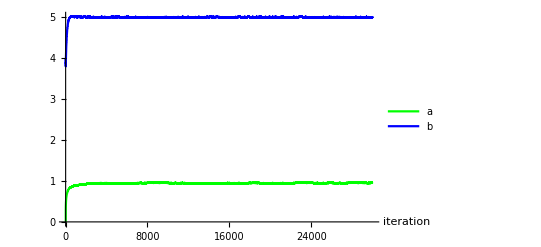

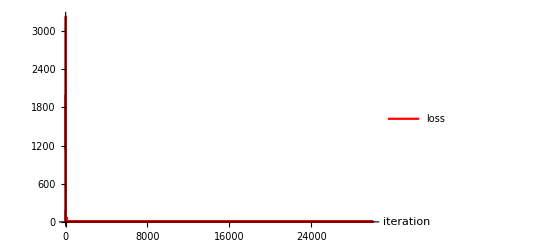

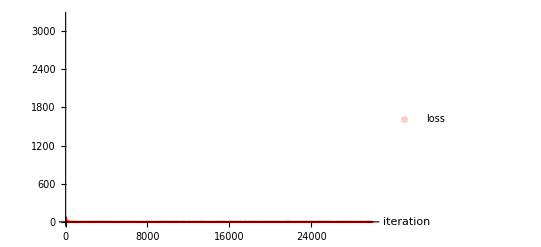

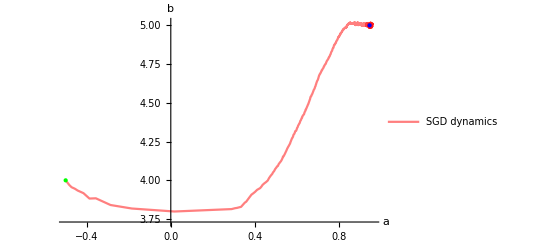

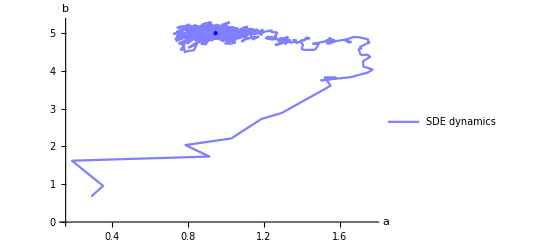

Part::partw: Part 1003 of {{0.290682,0.672108},{0.302523,0.706905},«7»,{0.381488,0.979201},«992»} does not exist.

Part::partw: Part 1004 of {{0.290682,0.672108},{0.302523,0.706905},«7»,{0.381488,0.979201},«992»} does not exist.

Part::partw: Part 1005 of {{0.290682,0.672108},{0.302523,0.706905},«7»,{0.381488,0.979201},«992»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

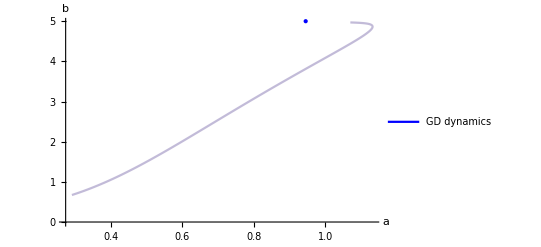

```mathematica
(* risultato: stima finale per a,b e confronto con quelli del modello vero *) 
Print["parametri stimati, SGD: ", v[[-1]]]
Print["parametri stimati, SDE: ", vc[[-1]]]
(*Print["parametri stimati, GD: ", vgd[[-1]]]*)
Print["a0, b0: ", a0," ",b0]
Print["atrue, btrue: ", atrue," ",btrue]
Print["areal, breal: ", areal," ",breal]
insamplesgd = loss[x,y]/.{x->v[[-1]][[1]],y->v[[-1]][[2]]};
insamplegd = loss[x,y]/.{x->vgd[[-1]][[1]],y->vgd[[-1]][[2]]};
insamplesde = loss[x,y]/.{x->vc[[-1]][[1]],y->vc[[-1]][[2]]};

outsamplesgd = lossp[x,y]/.{x->v[[-1]][[1]],y->v[[-1]][[2]]};
outsamplegd = lossp[x,y]/.{x->vgd[[-1]][[1]],y->vgd[[-1]][[2]]};
outsamplesde = lossp[x,y]/.{x->vc[[-1]][[1]],y->vc[[-1]][[2]]};

Print["In-sample error, SGD: ", insamplesgd," "]
Print["In-sample error, GD: ", insamplegd," "]
Print["In-sample error, SDE: ", insamplesde," "]

Print["Out-of-sample error, SGD: ", outsamplesgd," "]
Print["Out-of-sample error, GD: ", outsamplegd," "]
Print["Out-of-sample error, SDE: ", outsamplesde," "]

(* nei plot ricordati di mettere i nomi degli assi, le unità di misura se servono ecc. *)
Show[
ListLinePlot[Table[{ite,v[[ite]][[1]]},{ite,1,maxite}],
AxesOrigin->{0,0},
AxesLabel->{"iteration",""} ,PlotLegends->{"a"},PlotStyle->{Green}],
ListLinePlot[Table[{ite,v[[ite]][[2]]},{ite,1,maxite}],AxesOrigin->{0,0},
PlotLegends->{"b"},PlotStyle->{Blue}],PlotRange->All
]



ListLinePlot[Table[{ite,lossvalues[[ite]]},{ite,1,maxite}],PlotLegends->{"loss"},PlotStyle->{Red},
AxesLabel->{"iteration",""},PlotRange->All]

ListPlot[Table[{ite,lossvalues[[ite]]},{ite,1,maxite}],PlotLegends->{"loss"},PlotStyle->{Red,Opacity[0.2]},
AxesLabel->{"iteration",""},PlotRange->All]

initial=Graphics[{PointSize[Large],Green,Point[{a0,b0}]}]; (*punto di partenza*)
psgd=ListLinePlot[Table[{v[[ite]][[1]],v[[ite]][[2]]},{ite,1,maxite}],PlotLegends->{"SGD dynamics"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[psgd,g,initial]

psde=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,1,maxtimes}],PlotLegends->{"SDE dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[psde,g,initial]

pgd=ListLinePlot[Table[{vgd[[ite]][[1]],vgd[[ite]][[2]]},{ite,1,maxtimes}],PlotLegends->{"GD dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[pgd,g,initial]
```